0.984657

0.173622

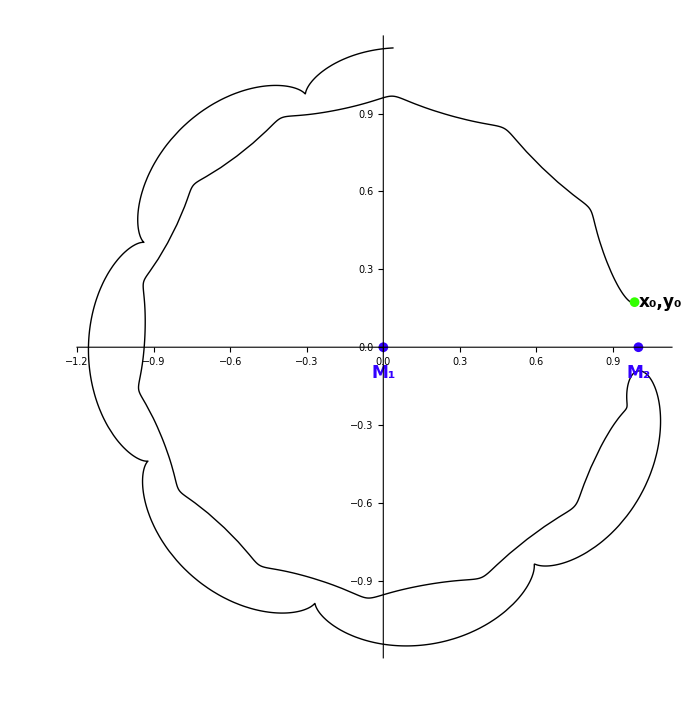

{{x[t]→1.04116,y[t]→0},{x[t]→0.95954,y[t]→0},{x[t]→-1.00008,y[t]→0}}

J==2 U-x'[t]^2-y'[t]^2

3.00153

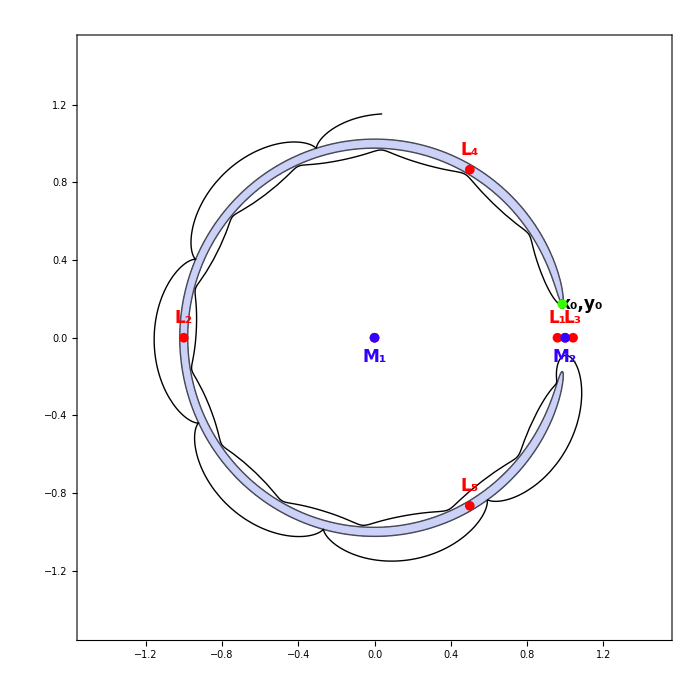

```mathematica
Clear["Global`*"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];

PMotion[mu1_,{x0_,y0_,vx0_,vy0_},tmax_,step_:10000]:=
Module[{rrule,Urule,eqMotion,r1,r2,mu,U},
rrule={
r1->(√((mu+x[t])^2+y[t]^2)),
r2->(√((-1+mu+x[t])^2+y[t]^2))};
Urule={U->(1-mu)/r1+mu/r2+0.5 (x[t]^2+y[t]^2)};
eqMotion=
{x''[t]-2y'[t]==D[U/.Urule/.rrule,x[t]],
y''[t]+2x'[t]==D[U/.Urule/.rrule,y[t]]};
NDSolve[{eqMotion/.mu->mu1,x[0]==x0,
y[0]==y0,x'[0]==vx0,y'[0]==vy0}//
Flatten,{x,y},{t,0,tmax},
MaxSteps->step]//Flatten];

Mgraph[fx_,fy_,t_,tfinal_,Opts___]:=
ParametricPlot[{fx[t],fy[t]}//Evaluate,
{t,0,tfinal},
Opts,
AspectRatio->Automatic,
DisplayFunction->Identity];

u=0.000204;
x0=R *Cos[p]/. R->0.5 Sqrt[3+(1-3 mu)^2]/. mu->u/. p->10°
y0=R *Sin[p]/. R->0.5 Sqrt[3+(1-3 mu)^2]/. mu->u/. p->10°
vx0=0.0;
vy0=0.0;
tfin=120.;

sol=PMotion[u,{x0,y0,vx0,vy0},tfin,10000];
fx[t_]:=x[t]/. sol;
fy[t_]:=y[t]/. sol;

pt1=Mgraph[fx,fy,t,tfin,PlotPoints->160,PlotStyle->Black,Epilog->{{AbsolutePointSize[7],Hue[0.7],Text[Style["\!\(\*SubscriptBox[\(M\), \(1\)]\)",Bold,17],{u,-0.1}],Text[Style["\!\(\*SubscriptBox[\(M\), \(2\)]\)",Bold,17],{1-u,-0.1}],{Point[{u,0}],Point[{1-u,0}]}},{AbsolutePointSize[7],Hue[0.3],Point[{x0,y0}]},Text[Style["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",Bold,17],{x0+0.1,y0}]},DisplayFunction->$DisplayFunction,ImageSize->700]

Urule=U->(1-mu)/r1+mu/r2+0.5 (x[t]^2+y[t]^2);
rrule={
r1->(√((mu+x[t])^2+y[t]^2)),
r2->(√((-1+mu+x[t])^2+y[t]^2))};

{L[5],L[4]}={{x[t]->0.5* (1-2 *mu),y[t]->-0.5* Sqrt[3]},{x[t]->0.5* (1-2* mu),y[t]->0.5 *Sqrt[3]}}/. {mu->u};
eq1=
D[U/.Urule/.rrule,x[t]]==0/.mu->u/.y[t]->0 ;
eq2=
D[U/.Urule/.rrule,y[t]]==0/.mu->u/.y[t]->0 ;
eq3=
FindRoot[eq1[[1]]/.mu->u/.
y[t]->0,{x[t],#}]&/@{1,0.9,-1} ;

{L[3],L[1],L[2]}=(Partition[#1,2]&)[Flatten[Outer[List,eq3,{y[t]->0}]]]
JLpt=(L[#1]&)/@Range[5];
ColumnForm[JLpt];

Lgraph=Graphics[{PointSize[0.01],RGBColor[1,0,0],{Point[{u,0}],Point[{1-u,0}]},{PointSize[0.01],RGBColor[1,0,0],Point/@({x[t],y[t]}/. JLpt)},(Text[Style[Subscript[L, #1],Bold,17],{x[t],y[t]+0.1}/. JLpt[[#1]]]&)/@Range[5]}]/. mu->u;
jacobi=J==-(Derivative[1][x][t]^2+Derivative[1][y][t]^2)+2 U
T=(jacobi/. Urule/. rrule/. mu->u/. y[t]->y0/. Derivative[1][x][t]->vx0/. x[t]->x0/. Derivative[1][y][t]->vy0)[[2]]
cont=ContourPlot[Evaluate[2 U/. Urule/. rrule/. mu->u],{x[t],-1.5,1.5},{y[t],-1.5,1.5},ContourShading->False,AspectRatio->Automatic,Contours->{T},PlotPoints->160,Epilog->{{AbsolutePointSize[7],Hue[0.7],Text[Style["\!\(\*SubscriptBox[\(M\), \(1\)]\)",Bold,17],{u,-0.1}],Text[Style["\!\(\*SubscriptBox[\(M\), \(2\)]\)",Bold,17],{1-u,-0.1}],{Point[{u,0}],Point[{1-u,0}]}},{AbsolutePointSize[7],Hue[0.3],Point[{x0,y0}]},Text[Style["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",Bold,17],{x0+0.1,y0}]},DisplayFunction->$DisplayFunction,ImageSize->700];
ev=Evaluate[2 U/. Urule/. rrule/. mu->u];
region=RegionPlot[ev<T,{x[t],-1.5,1.5},{y[t],-1.5,1.5},AspectRatio->Automatic,PlotPoints->300,Epilog->{{AbsolutePointSize[7],Hue[0.7],Text[Style["\!\(\*SubscriptBox[\(M\), \(1\)]\)",Bold,17],{u,-0.1}],Text[Style["\!\(\*SubscriptBox[\(M\), \(2\)]\)",Bold,17],{1-u,-0.1}],{Point[{u,0}],Point[{1-u,0}]}},{AbsolutePointSize[7],Hue[0.3],Point[{x0,y0}]},Text[Style["\!\(\*SubscriptBox[\(x\), \(0\)]\),\!\(\*SubscriptBox[\(y\), \(0\)]\)",Bold,17],{x0+0.1,y0}]},DisplayFunction->$DisplayFunction,ImageSize->700];
gra=Show[region,pt1,cont,Lgraph,DisplayFunction->$DisplayFunction,ImageSize->700]
```